```mathematica
Clear[h,δ,A1,D1,S1,M1,P1,G1,m,E1,λmax,qmax,K];
h=1;
A1=0;
E1=0.0001;
D1=0.001;
S1=100;
δ=E1^2/(D1 S1);
M1=35.01;
P1=7.02;
G1=1/3;

a = A1/S1;

xg=1.0;
Bo=xg*G1/S1;
K1=1;
B=0.0;
Bi=1+B K;
m=(M1 K1 Bi)/(P1 S1)

R = 10^-3;


(*FindRoot[K==S1 (qmax^2(2*h^3)-Bo h^3-δ h^3 (h+K)^-3)/(M1 P1 h^2 (h+K)^-2),{K,0.01}]*)
qmax[Bo_,h_]:=Sqrt[(a h^-1 -Bo h^3 + R h^3+δ h^3 (Bi h+K1)^-3+m h^2 (Bi h+K1)^-2)/(2 (h^3))]

Print["--------------------------------"]
Print["Maximizing WAVENUMBER/Frequency"]
qmax[Bo,1]
Print["--------------------------------"]
Print["Maximizing wavelength"]
L=2 π/qmax[Bo,1]
Print["--------------------------------"]
Bo;
m;
Bi;
```

0.0498718

--------------------------------

Maximizing WAVENUMBER/Frequency

0.0711851

--------------------------------

Maximizing wavelength

88.2655

--------------------------------

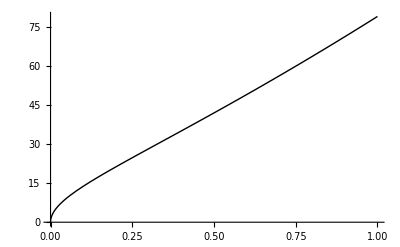

```mathematica
Needs["PlotLegends`"];
xh=1;
λg=Plot[N[2 π/qmax[Bo,xh],3],{xh,0.00001,1},PlotRange->Full,PlotStyle->Directive[Black,Thick],BaseStyle->{FontWeight->"Plain",FontSize->18}]
```